Read an example JSON string:

```mathematica
circles=ImportString["[[0.375,0.4375,0.125],[0.75,0.3125,0.125],[1.0,0.9375,0.1875],[0.4375,0.75,0.125],[0.1875,0.0625,0.3125],[0.5625,0.625,0.1875]]","JSON"];
```

Create an image showing the geometry:

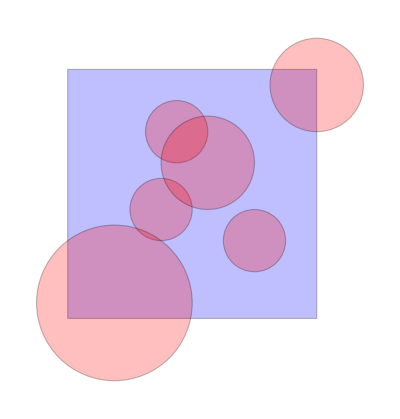

```mathematica
image=Graphics[{
EdgeForm[{Thin,Black}],
Opacity[0.25],
Blue,Rectangle[],
Red,Apply[Disk[{#1,#2},#3]&, circles,2]
},ImageSize->400]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"img","circles.png"}],image];
```